```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames[]
```

{1200.nb,1200_upravene.nb,1400.nb,1500.nb,1600.nb,1800.nb,2000.nb,final-NG-1200-100SK-27BTDC.pdf,NG-1200-100SK-27BTDC.TXT,NG-1400-100SK-27BTDC.TXT,NG-1500-100SK-27BTDC.TXT,NG-1600-100SK-27BTDC.TXT,NG-1800-100SK-27BTDC.TXT,NG-2000-100SK-27BTDC.TXT,piatystlpec-NG-1200-100SK-27BTDC.TXT.txt,piatystlpec-NG-1200-100SK-27BTDC.TXT.xls,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls,tretistlpec-NG-1200-100SK-27BTDC.TXT.txt,tretistlpec-NG-1200-100SK-27BTDC.TXT.xls}

```mathematica
subor="NG-1500-100SK-27BTDC.TXT";
```

```mathematica
a=ReadList[subor,Table[Number,{5}]];
```

```mathematica
prvystlpec=a[[All,1]];
druhystlpec=a[[All,2]];
tretistlpec=a[[All,3]];
stvrtystlpec=a[[All,4]];
piatystlpec=a[[All,5]];
```

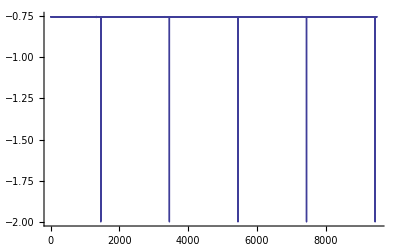

```mathematica
ListLinePlot[druhystlpec[[1;;9500;;1]],PlotRange->All]
```

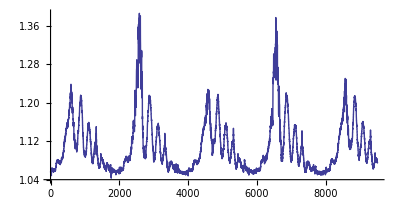

```mathematica
ListLinePlot[tretistlpec[[1;;9500;;1]],AspectRatio->0.5]
```

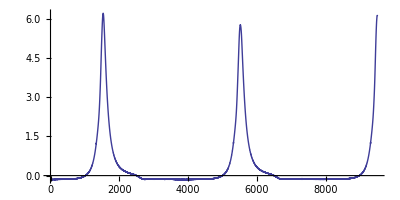

```mathematica
ListLinePlot[stvrtystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

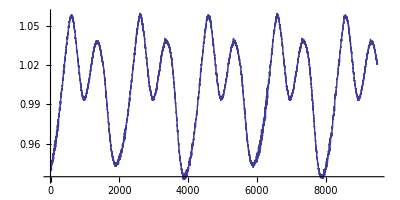

```mathematica
ListLinePlot[piatystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

```mathematica
Length[prvystlpec]
```

1048576

```mathematica
pom3={};
Do[
If[druhystlpec[[i]]<-1.8,AppendTo[pom3, i]],{i,1,Length[druhystlpec]}];
pom4={};
Do[
If[pom3[[i+1]]-pom3[[i]]>10,AppendTo[pom4,pom3[[i]]]],{i,1, Length[pom3]-1}];
pom4
```

{1463,3455,5448,7439,9432,11424,13416,15408,17401,19393,21385,23377,25369,27361,29354,31346,33339,35331,37324,39317,41309,43302,45294,47287,49279,51271,53264,55256,57248,59240,61232,63224,65216,67207,69199,71191,73184,75176,77169,79162,81155,83147,85140,87133,89125,91117,93109,95101,97093,99084,101077,103069,105061,107053,109045,111037,113030,115021,117013,119005,120997,122990,124982,126975,128967,130960,132953,134946,136939,138932,140925,142918,144911,146904,148897,150889,152882,154875,156867,158859,160851,162843,164835,166827,168819,170810,172802,174794,176785,178777,180768,182759,184750,186741,188733,190724,192715,194707,196699,198691,200683,202675,204668,206660,208653,210645,212637,214630,216622,218614,220606,222599,224591,226583,228576,230569,232562,234555,236548,238541,240534,242528,244521,246514,248508,250501,252495,254488,256481,258475,260468,262461,264454,266447,268440,270433,272426,274419,276411,278403,280396,282388,284380,286372,288365,290357,292349,294341,296333,298325,300318,302310,304303,306296,308289,310281,312274,314266,316258,318250,320243,322234,324227,326218,328211,330202,332194,334186,336178,338169,340162,342154,344146,346138,348131,350123,352115,354107,356099,358090,360083,362075,364067,366059,368052,370044,372036,374028,376020,378013,380006,381998,383991,385983,387976,389969,391962,393954,395947,397940,399932,401925,403917,405910,407902,409895,411887,413880,415872,417865,419857,421849,423841,425834,427826,429818,431810,433802,435795,437787,439779,441772,443764,445757,447749,449741,451734,453726,455719,457711,459703,461695,463687,465679,467671,469663,471656,473649,475641,477634,479626,481618,483610,485602,487594,489586,491578,493571,495563,497557,499550,501544,503537,505530,507523,509516,511508,513501,515493,517486,519478,521470,523462,525455,527447,529439,531432,533424,535417,537409,539401,541393,543386,545377,547369,549362,551354,553347,555339,557331,559324,561316,563308,565300,567292,569284,571277,573270,575262,577255,579248,581240,583233,585226,587219,589212,591205,593198,595190,597183,599175,601168,603161,605154,607147,609139,611132,613125,615118,617111,619103,621096,623089,625082,627075,629068,631060,633053,635046,637039,639032,641024,643016,645008,647001,648993,650985,652977,654969,656960,658952,660944,662936,664927,666919,668911,670903,672896,674888,676880,678872,680865,682857,684849,686842,688835,690827,692820,694813,696805,698797,700790,702782,704774,706766,708758,710750,712742,714734,716726,718718,720710,722701,724693,726685,728676,730668,732660,734652,736643,738635,740627,742619,744611,746603,748595,750587,752578,754570,756562,758554,760546,762538,764530,766522,768514,770506,772498,774491,776484,778477,780469,782463,784456,786450,788443,790436,792429,794422,796415,798408,800400,802392,804384,806377,808369,810362,812354,814346,816338,818330,820322,822315,824307,826300,828292,830284,832276,834268,836261,838253,840246,842238,844231,846223,848215,850207,852199,854191,856182,858175,860166,862158,864150,866142,868134,870126,872118,874110,876102,878094,880086,882077,884069,886062,888054,890046,892039,894032,896025,898017,900010,902003,903995,905988,907980,909972,911964,913957,915949,917942,919934,921927,923920,925913,927906,929899,931892,933885,935877,937870,939863,941856,943849,945842,947835,949828,951820,953813,955805,957798,959790,961783,963775,965767,967760,969752,971744,973737,975729,977721,979713,981705,983698,985690,987682,989674,991666,993658,995651,997643,999635,1001627,1003619,1005611,1007604,1009596,1011589,1013581,1015574,1017566,1019559,1021551,1023544,1025536,1027528,1029520,1031512,1033504,1035496,1037488,1039480,1041472,1043465,1045457}

```mathematica
Length[pom4]
```

525

```mathematica
cyklus={};
Table[AppendTo[cyklus,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus//Length
```

261

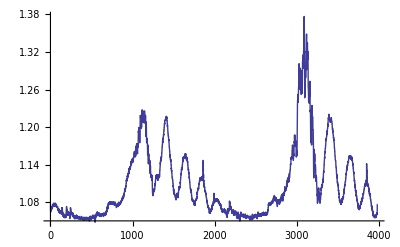
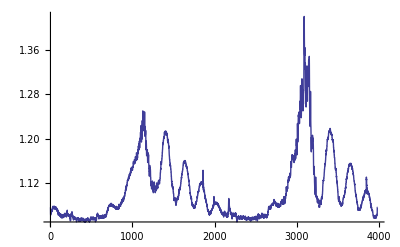
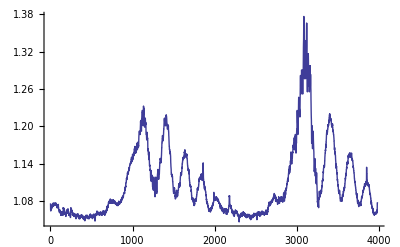
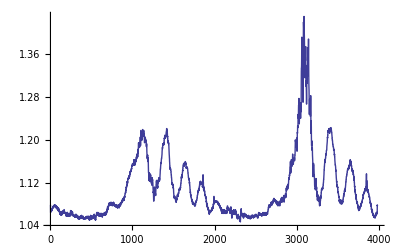
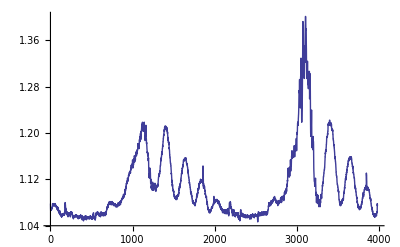
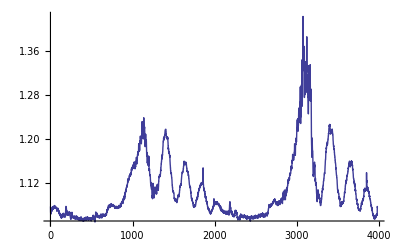
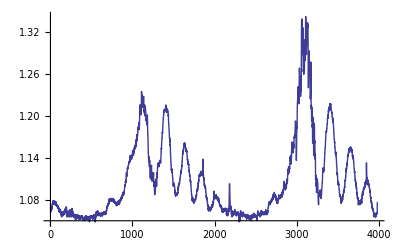
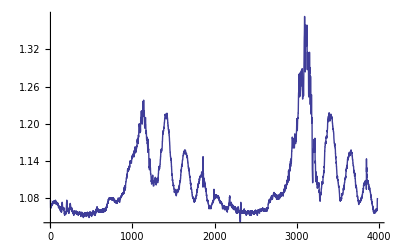

```mathematica
Table[ListLinePlot[cyklus[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]
```

{3985,3986,3985,3986,3985,3985,3986,3986,3987,3986,3986,3985,3986,3985,3985,3984,3985,3986,3987,3986,3987,3985,3985,3984,3986,3985,3985,3985,3985,3986,3986,3986,3987,3987,3987,3987,3986,3987,3985,3985,3985,3984,3985,3984,3983,3983,3984,3984,3985,3985,3986,3986,3986,3985,3986,3985,3987,3987,3987,3988,3987,3988,3988,3988,3987,3987,3987,3987,3985,3986,3985,3986,3985,3985,3986,3987,3986,3986,3985,3985,3985,3985,3985,3984,3986,3985,3986,3985,3984,3986,3985,3986,3985,3986,3986,3986,3987,3986,3987,3986,3986,3986,3986,3986,3985,3986,3985,3985,3986,3986,3986,3985,3986,3986,3985,3985,3985,3987,3986,3985,3985,3985,3986,3987,3988,3987,3987,3986,3986,3985,3986,3985,3986,3986,3985,3985,3986,3986,3985,3986,3985,3985,3987,3986,3986,3987,3987,3987,3986,3986,3987,3986,3987,3987,3986,3987,3987,3986,3987,3986,3985,3986,3985,3984,3985,3984,3985,3986,3985,3986,3985,3987,3986,3986,3986,3985,3985,3985,3985,3985,3984,3984,3985,3984,3985,3985,3985,3984,3985,3985,3985,3985,3985,3987,3986,3988,3988,3987,3987,3986,3985,3986,3986,3985,3985,3986,3986,3985,3986,3986,3986,3985,3985,3984,3985,3985,3985,3985,3985,3985,3984,3986,3986,3987,3986,3986,3986,3985,3986,3986,3987,3987,3987,3986,3987,3987,3987,3986,3986,3986,3986,3986,3985,3986,3985,3986,3985,3985,3986,3985,3985,3986,3986,3986,3986,3986,3985,3985,3985,3985,3986}

```mathematica
pom5=Min[Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]];
pom6=Table[Take[cyklus[[i]],pom5],{i,1,Length[cyklus]}];
```

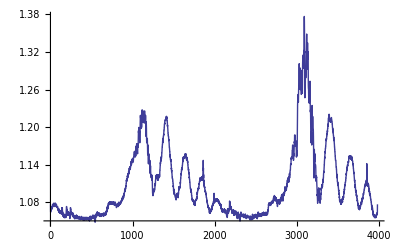
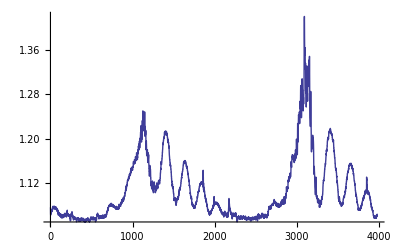
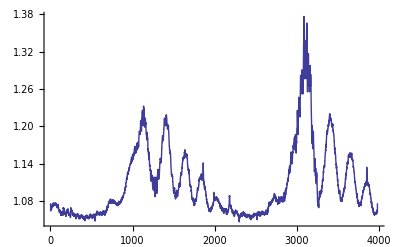
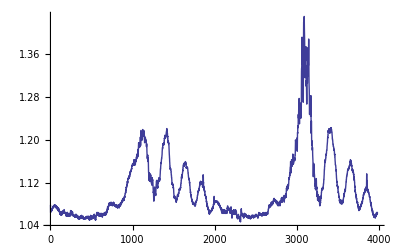
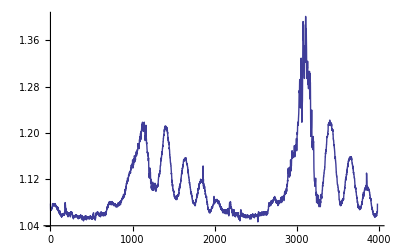
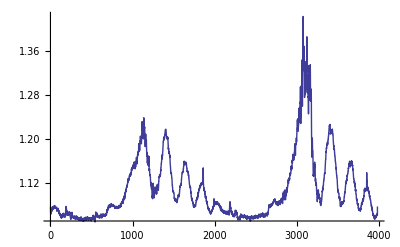
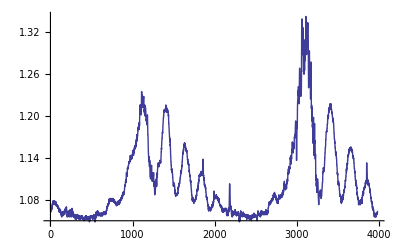
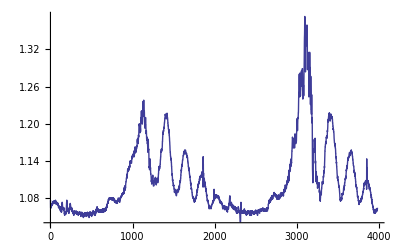

```mathematica
Table[ListLinePlot[pom6[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[pom6]//Dimensions
```

{3983,261}

```mathematica
priemernehodnotydruhystlpec=Table[Mean[pom6[[All,i]]],{i,1,3983}];
```

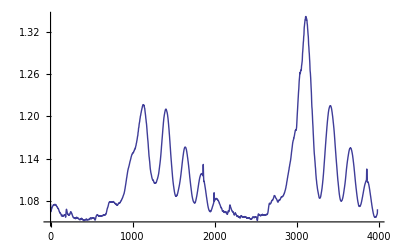

```mathematica
ListLinePlot[priemernehodnotydruhystlpec]
```

```mathematica
cyklus3={};
cyklus4={};
cyklus5={};
Table[AppendTo[cyklus3,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus4,stvrtystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus5,piatystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus3//Length
```

261

```mathematica
Table[ListLinePlot[cyklus3[[i]],PlotRange->All],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

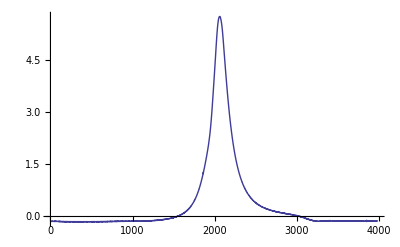
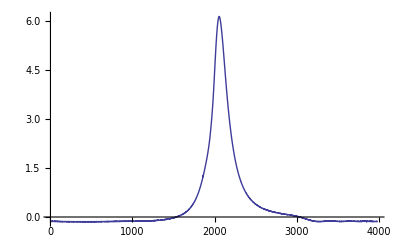
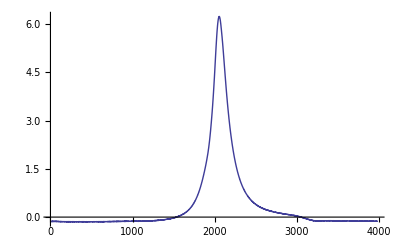
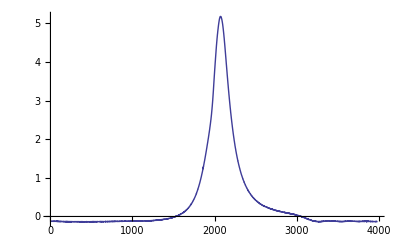
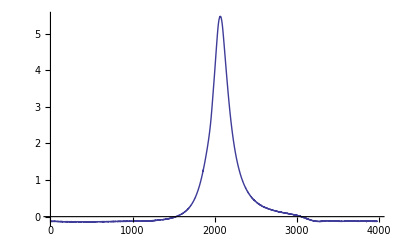
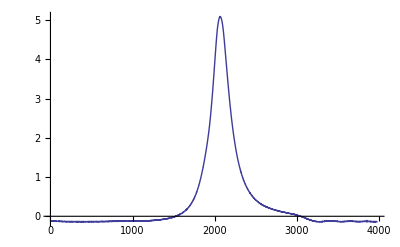
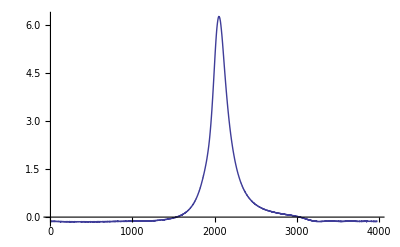
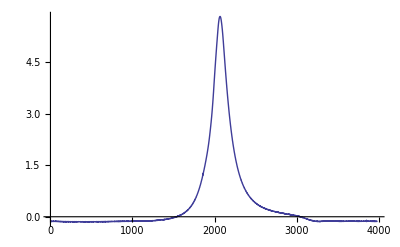

```mathematica
Table[ListLinePlot[cyklus4[[i]],PlotRange->All],{i,1,10}]
```

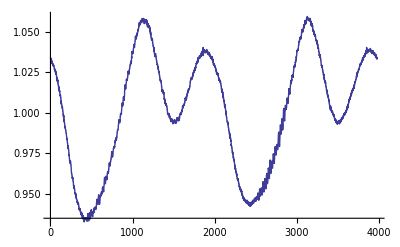
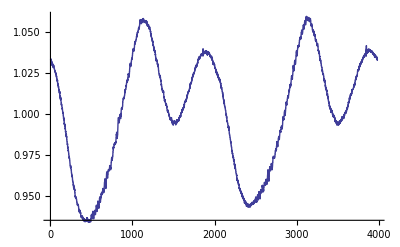
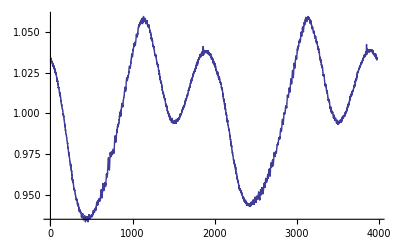
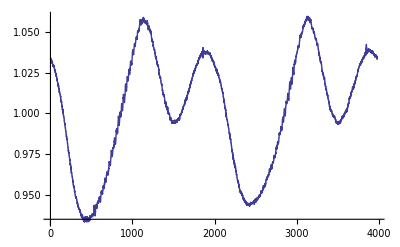
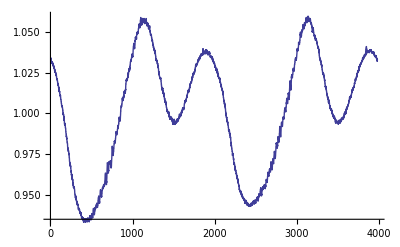
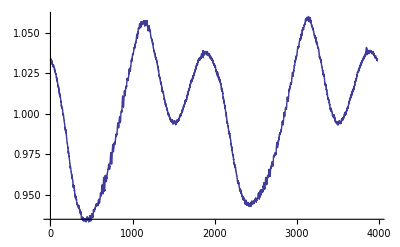
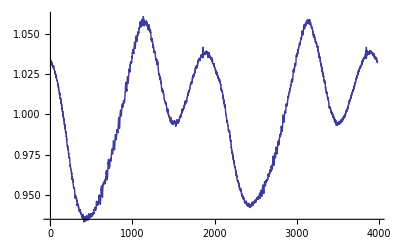
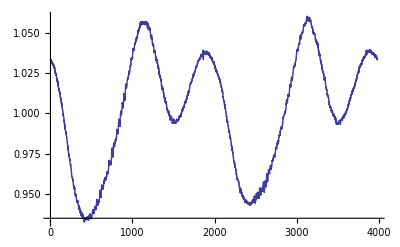

```mathematica
Table[ListLinePlot[cyklus5[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus3[[i]]],{i,1,Length[cyklus]}]
```

{3985,3986,3985,3986,3985,3985,3986,3986,3987,3986,3986,3985,3986,3985,3985,3984,3985,3986,3987,3986,3987,3985,3985,3984,3986,3985,3985,3985,3985,3986,3986,3986,3987,3987,3987,3987,3986,3987,3985,3985,3985,3984,3985,3984,3983,3983,3984,3984,3985,3985,3986,3986,3986,3985,3986,3985,3987,3987,3987,3988,3987,3988,3988,3988,3987,3987,3987,3987,3985,3986,3985,3986,3985,3985,3986,3987,3986,3986,3985,3985,3985,3985,3985,3984,3986,3985,3986,3985,3984,3986,3985,3986,3985,3986,3986,3986,3987,3986,3987,3986,3986,3986,3986,3986,3985,3986,3985,3985,3986,3986,3986,3985,3986,3986,3985,3985,3985,3987,3986,3985,3985,3985,3986,3987,3988,3987,3987,3986,3986,3985,3986,3985,3986,3986,3985,3985,3986,3986,3985,3986,3985,3985,3987,3986,3986,3987,3987,3987,3986,3986,3987,3986,3987,3987,3986,3987,3987,3986,3987,3986,3985,3986,3985,3984,3985,3984,3985,3986,3985,3986,3985,3987,3986,3986,3986,3985,3985,3985,3985,3985,3984,3984,3985,3984,3985,3985,3985,3984,3985,3985,3985,3985,3985,3987,3986,3988,3988,3987,3987,3986,3985,3986,3986,3985,3985,3986,3986,3985,3986,3986,3986,3985,3985,3984,3985,3985,3985,3985,3985,3985,3984,3986,3986,3987,3986,3986,3986,3985,3986,3986,3987,3987,3987,3986,3987,3987,3987,3986,3986,3986,3986,3986,3985,3986,3985,3986,3985,3985,3986,3985,3985,3986,3986,3986,3986,3986,3985,3985,3985,3985,3986}

```mathematica
pom5=Min[Table[Length[cyklus3[[i]]],{i,1,Length[cyklus3]}]];
cyklus3orezany=Table[Take[cyklus3[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus4orezany=Table[Take[cyklus4[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus5orezany=Table[Take[cyklus5[[i]],pom5],{i,1,Length[cyklus3]}];
```

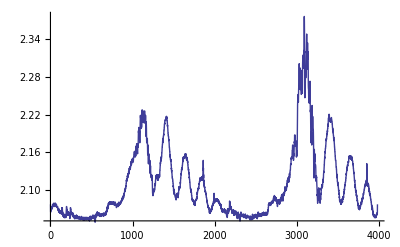
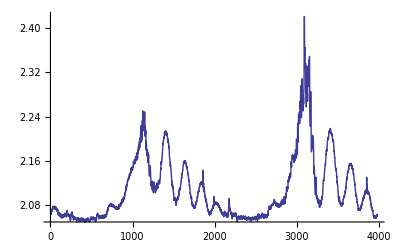
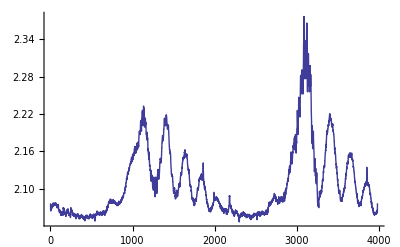
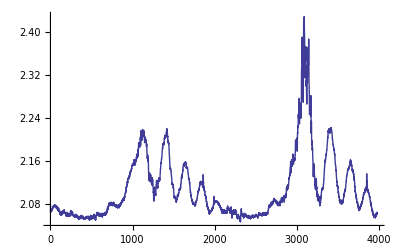
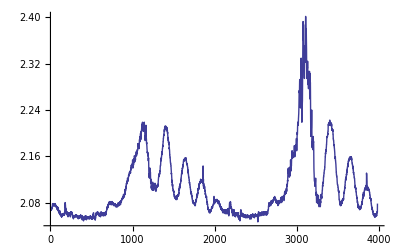
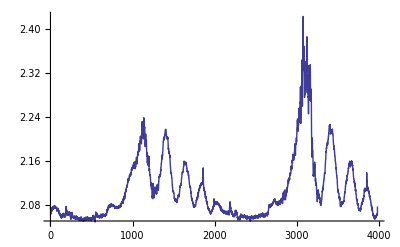
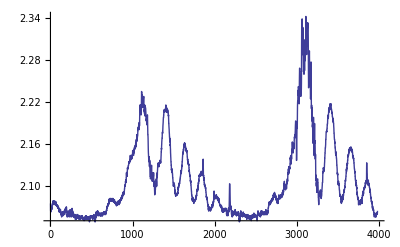
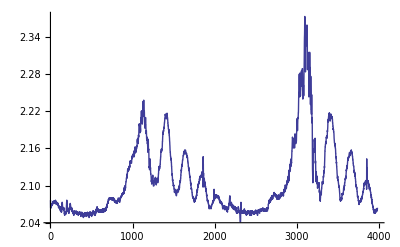

```mathematica
Table[ListLinePlot[cyklus3orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

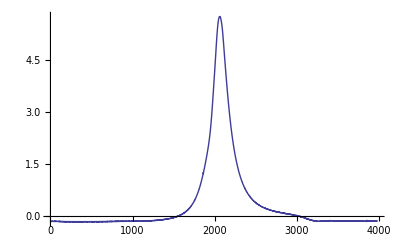
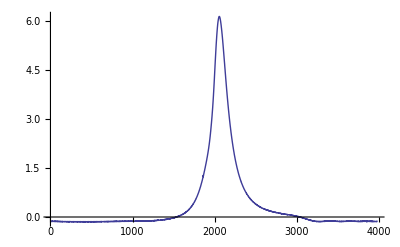
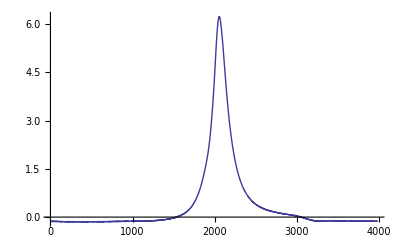
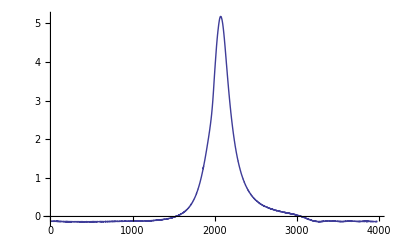
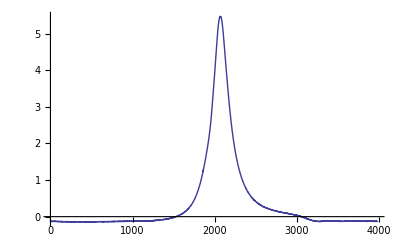
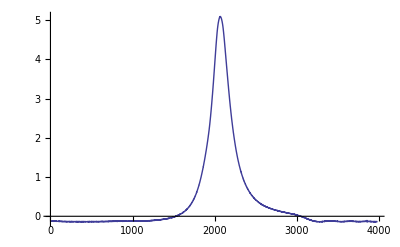
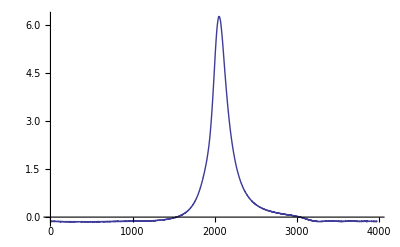
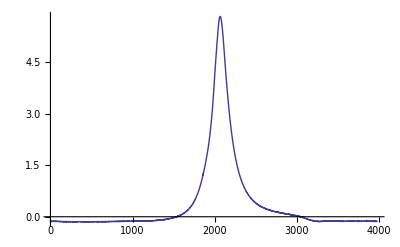

```mathematica
Table[ListLinePlot[cyklus4orezany[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[cyklus3orezany]//Dimensions
```

{3983,261}

```mathematica
priemernehodnoty3stlpec=Table[Mean[cyklus3orezany[[All,i]]],{i,1,3983}];
priemernehodnoty4stlpec=Table[Mean[cyklus4orezany[[All,i]]],{i,1,3983}];
priemernehodnoty5stlpec=Table[Mean[cyklus5orezany[[All,i]]],{i,1,3983}];
```

```mathematica
Length[priemernehodnoty4stlpec]
```

3983

```mathematica
k=0;
x=Table[k=k+720/Length[priemernehodnoty4stlpec]//N,{Length[priemernehodnoty4stlpec]}];
```

```mathematica
obr3=ListLinePlot[priemernehodnoty3stlpec]
```

-Graphics-

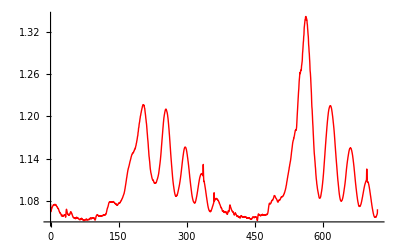

```mathematica
dataobr3=Transpose@{x,priemernehodnoty3stlpec};
obr3a1500=ListLinePlot[dataobr3,PlotStyle->Red]
```

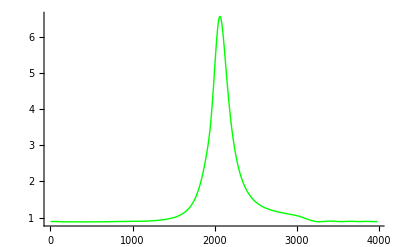

```mathematica
obr4=ListLinePlot[priemernehodnoty4stlpec+1.0335, PlotStyle->Green,PlotRange->All]
```

```mathematica
priemernehodnoty4stlpecnove=priemernehodnoty4stlpec+1.1335;
```

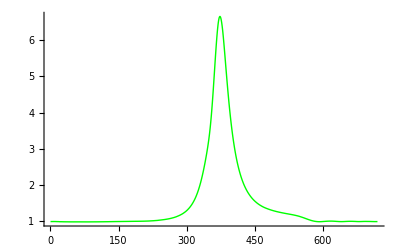

```mathematica
dataobr4=Transpose@{x,priemernehodnoty4stlpecnove};
obr1500a=ListLinePlot[dataobr4,PlotStyle->Green,PlotRange->All]
```

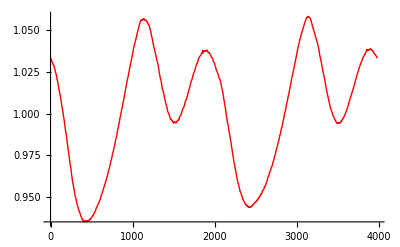

```mathematica
obr5=ListLinePlot[priemernehodnoty5stlpec,PlotStyle->Red]
```

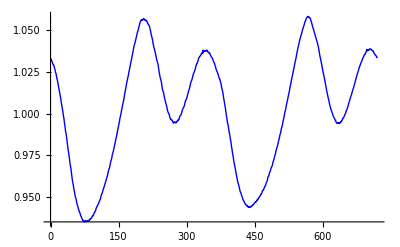

```mathematica
dataobr5=Transpose@{x,priemernehodnoty5stlpec};
obr1500a=ListLinePlot[dataobr5,PlotStyle->Blue]
```

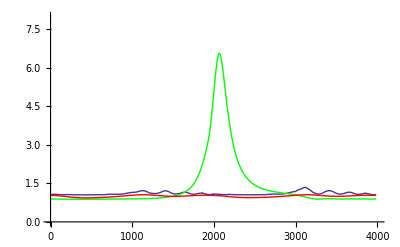

```mathematica
Show[{obr3,obr4,obr5},PlotRange->{{0,4000},{0,8}},AxesOrigin->{0,0}]
```

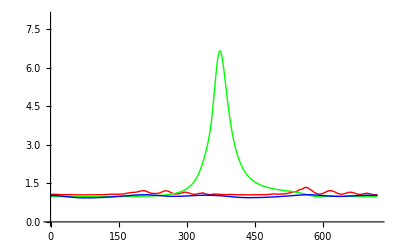

```mathematica
obrfinala=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0,8}},AxesOrigin->{0,0}]
```

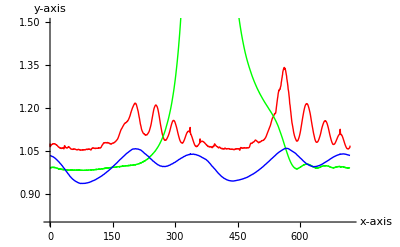

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},LabelStyle->(FontSize->14),AxesLabel->{"x-axis","y-axis"}]
```

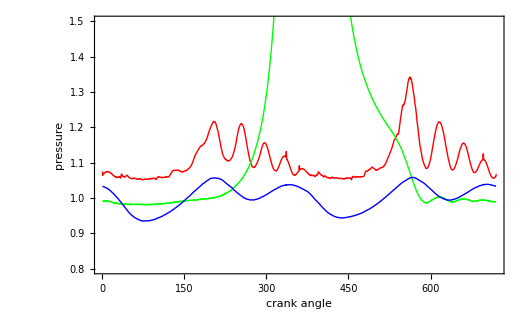

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},PlotRange->{{-3,0},{0,1}},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

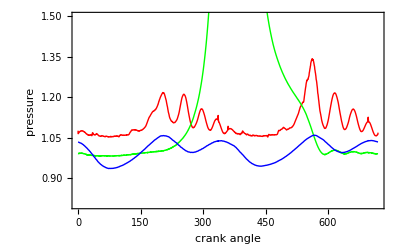

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```